```mathematica
a=-Pi/4;
b=Pi/4;
c=-2.0;
A[t_]=t-1;
B[t_]=ArcTan[t/2];
K[ξ_,t_]=Sin[ξ+t^2];
f[t_]=Sin[t]^2;
NN=100;

UG= Table[i,{i,a,b,(b-a)/(NN-1)}]; 
AA=A[UG];
BB=B[UG];

F[t_]=f[t]-c*B[t]-c*Integrate[K[ξ,t],{ξ,a,b}];
FF=F[UG];
```

```mathematica
DD=Table[0.,{NN},{NN}];
For[j=1,j<=NN,j++,
(*Preparation for the natural spline making*)
w=Table[{UG[[k]],0.0},{k,1,NN}]; (*Pairs of values {grid point, function values}*)
w[[j,2]]=1; (*Definition of natural spline as a spline through only 1 nodes with value 1 and others are 0*)(*Interpolation polynom*)
S=Interpolation[w];
For[i=1,i<NN,i++,
DD[[i+1,j]]=DD[[i,j]]+Integrate[S[x],{x,UG[[i]],UG[[i+1]]}];
];
];


(*Array of uniform weight vector*)
α=Table[0,{NN}];
(*Filling vector α*)
For[j=1, j<=NN, j++,
(*Preparation for the natural spline making*)
w=Table[{UG[[i]],0.0},{i,1,NN}]; (*Pairs of values {grid point, function values}*)
w[[j,2]]=1; (*Definition of natural spline as a spline through only 1 nodes with value 1 and others are 0*)(*Interpolation polynom*)
S=Interpolation[w,Method->"Spline"];
α[[j]]=NIntegrate[S[x], {x,a,b}];
]
```

0.5 | 0.500026
0.359134 | 0.359134
0.22968 | 0.22968
0.122125 | 0.122125
0.045184 | 0.0451839
0.00508928 | 0.00508911
0.00508928 | 0.00508893
0.045184 | 0.0451832
0.122125 | 0.122123
0.22968 | 0.229674
0.359134 | 0.359108
0.5 | 0.495651

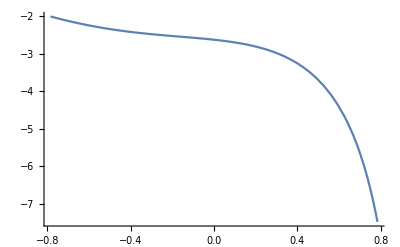

```mathematica
GG=Table[0.,{NN},{NN}];
For[i=1,i<=NN,i++,
For[j=1,j<=NN,j++,
GG[[i,j]]=Sum[α[[k]]*K[UG[[k]],UG[[i]]]*DD[[k,j]],{k,1,NN}];
];
];

Lhs=Table[0.,{NN},{NN}];
Rhs=Table[0.,{NN}];
For[i=1,i<=NN,i++,
For[j=1,j<=NN,j++,
If[i==j,
Lhs[[i,j]]=AA[[i]]+BB[[i]]*DD[[i,j]]+GG[[i,j]],
Lhs[[i,j]]=BB[[i]]*DD[[i,j]]+GG[[i,j]]
];
];
Rhs[[i]]=FF[[i]];
];
λ=LinearSolve[Lhs,Rhs];
NSol=Table[c+Sum[DD[[i,j]]*λ[[j]],{j,1,NN}],{i,1,NN}];
YAn=Interpolation[Table[{UG[[i]],NSol[[i]]},{i,1,NN}],Method->"Spline"];

SolutionCheck=Table[{f[z] //N,A[z]*YAn'[z]+B[z]*YAn[z]+NIntegrate[YAn[ζ]*K[ζ,z],{ζ,a,b}]},{z,a,b,(b-a)/11}];
SolutionCheck //TableForm
Plot[YAn[x],{x,a,b},PlotRange->All]
```